```mathematica
Table[
Labeled[allGraphs5[k,"graph"],k],
{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&& TreeGraphQ[g]&& Max[VertexDegree[g]]≤3 && MyPlanar[allGraphs5,#]] &]}
]
```

{-Graphics-28432,-Graphics-26982,-Graphics-26974,-Graphics-26256,-Graphics-26254,-Graphics-26248,-Graphics-22842,-Graphics-22608,-Graphics-22114,-Graphics-21880,-Graphics-20736,-Graphics-20664,-Graphics-20656,-Graphics-20502,-Graphics-20424,-Graphics-20422,-Graphics-20416,-Graphics-20008,-Graphics-19962,-Graphics-19954,-Graphics-19938,-Graphics-19936,-Graphics-19930,-Graphics-19800,-Graphics-19774,-Graphics-19722,-Graphics-19720,-Graphics-19714,-Graphics-9720,-Graphics-8992,-Graphics-7542,-Graphics-7534,-Graphics-6814,-Graphics-6808,-Graphics-3240,-Graphics-3168,-Graphics-3006,-Graphics-2512,-Graphics-2440,-Graphics-1080,-Graphics-1054,-Graphics-1008,-Graphics-1000,-Graphics-984,-Graphics-982,-Graphics-976,-Graphics-846,-Graphics-820,-Graphics-768,-Graphics-766}

```mathematica
Length[%]
```

50

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&& TreeGraphQ[g]&& Max[VertexDegree[g]]≤3 ] &]//Length
```

120

```mathematica
ShowGraph5Least[7738]
```

-Graphics-77380

```mathematica
eqs=Table[
Symbol["t"<>ToString[k]]==allGraphs5[k,"colofourrealnull"],
{k,Select[Keys[allGraphs5],!MemberQ[{7738},#]&&With[{g=allGraphs5[#,"graph"]}, TreeGraphQ[g]] &]}
]
```

{t29160==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5+n145x2x3-n14x2x3x5-n15x2x3x4+n1x2x3x4x5,t29646==-n12345+n1234x5+n1235x4-n123x4x5+n145x23-n14x23x5-n15x23x4+n1x23x4x5,t29826==n12345-n1234x5-n15x234+n1x234x5,t29888==-n12345+n1x2345,t29706==n12345-n1235x4-n14x235+n1x235x4,t29648==n12345-n123x45-n145x23+n1x23x45,t29322==-n12345+n1234x5+n1245x3-n124x3x5+n135x24-n13x24x5-n15x24x3+n1x24x3x5,t29378==n12345-n1245x3-n13x245+n1x245x3,t29328==n12345-n124x35-n135x24+n1x24x35,t29214==-n12345+n1235x4+n1245x3-n125x3x4+n134x25-n13x25x4-n14x25x3+n1x25x3x4,t29232==n12345-n125x34-n134x25+n1x25x34,t29178==-n12345+n1234x5+n125x34-n12x34x5+n1345x2-n134x2x5-n15x2x34+n1x2x34x5,t29186==n12345-n12x345-n1345x2+n1x2x345,t29166==-n12345+n1235x4+n124x35-n12x35x4+n1345x2-n135x2x4-n14x2x35+n1x2x35x4,t29162==-n12345+n123x45+n1245x3-n12x3x45+n1345x2-n13x2x45-n145x2x3+n1x2x3x45,t29920==-n12345+n1235x4+n1245x3-n125x3x4+n1345x2-n135x2x4-n145x2x3+n15x2x3x4,t30406==n12345-n1235x4-n145x23+n15x23x4,t30586==-n12345+n15x234,t30082==n12345-n1245x3-n135x24+n15x24x3,t29938==n12345-n125x34-n1345x2+n15x2x34,t29128==n12345-n1234x5-n1x2345+n1x234x5,t28947==-n12345+n1234x5+n1235x4-n123x4x5+n14x235-n14x23x5-n1x235x4+n1x23x4x5,t28918==-n12345+n1234x5+n123x45-n123x4x5+n145x23-n14x23x5-n1x23x45+n1x23x4x5,t28621==-n12345+n1234x5+n1245x3-n124x3x5+n13x245-n13x24x5-n1x245x3+n1x24x3x5,t28596==-n12345+n1234x5+n124x35-n124x3x5+n135x24-n13x24x5-n1x24x35+n1x24x3x5,t28458==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n134x25+n134x2x5+n13x25x4-n13x2x4x5+n14x25x3-n14x2x3x5-n1x25x3x4+n1x2x3x4x5,t28476==-n12345+n1234x5+n125x34-n12x34x5+n134x25-n134x2x5-n1x25x34+n1x2x34x5,t28453==-n12345+n1234x5+n12x345-n12x34x5+n1345x2-n134x2x5-n1x2x345+n1x2x34x5,t28434==n12345-n1234x5-n1235x4+n123x4x5-n124x35+n124x3x5+n12x35x4-n12x3x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5+n14x2x35-n14x2x3x5-n1x2x35x4+n1x2x3x4x5,t28432==n12345-n1234x5-n123x45+n123x4x5-n1245x3+n124x3x5+n12x3x45-n12x3x4x5-n1345x2+n134x2x5+n13x2x45-n13x2x4x5+n145x2x3-n14x2x3x5-n1x2x3x45+n1x2x3x4x5,t31438==-n12345+n1234x5+n1245x3-n124x3x5+n1345x2-n134x2x5-n145x2x3+n14x2x3x5,t31924==n12345-n1234x5-n145x23+n14x23x5,t31984==-n12345+n14x235,t31492==n12345-n1245x3-n134x25+n14x25x3,t31444==n12345-n124x35-n1345x2+n14x2x35,t32198==n12345-n1245x3-n1345x2+n145x2x3,t32684==-n12345+n145x23,t31224==n12345-n1234x5-n14x235+n14x23x5,t30735==-n12345+n1234x5+n1245x3-n124x3x5+n134x25-n134x2x5-n14x25x3+n14x2x3x5,t30711==-n12345+n1234x5+n124x35-n124x3x5+n1345x2-n134x2x5-n14x2x35+n14x2x3x5,t27549==-n12345+n1234x5+n1235x4-n123x4x5+n15x234-n15x23x4-n1x234x5+n1x23x4x5,t27610==n12345-n1235x4-n1x2345+n1x235x4,t27460==-n12345+n1235x4+n123x45-n123x4x5+n145x23-n15x23x4-n1x23x45+n1x23x4x5,t27054==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5+n15x24x3-n15x2x3x4-n1x24x3x5+n1x2x3x4x5,t27109==-n12345+n1235x4+n1245x3-n125x3x4+n13x245-n13x25x4-n1x245x3+n1x25x3x4,t27060==-n12345+n1235x4+n124x35-n12x35x4+n135x24-n135x2x4-n1x24x35+n1x2x35x4,t27036==-n12345+n1235x4+n125x34-n125x3x4+n134x25-n13x25x4-n1x25x34+n1x25x3x4,t26982==n12345-n1234x5-n1235x4+n123x4x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5+n15x2x34-n15x2x3x4-n1x2x34x5+n1x2x3x4x5,t26989==-n12345+n1235x4+n12x345-n12x35x4+n1345x2-n135x2x4-n1x2x345+n1x2x35x4,t26974==n12345-n1235x4-n123x45+n123x4x5-n1245x3+n125x3x4+n12x3x45-n12x3x4x5-n1345x2+n135x2x4+n13x2x45-n13x2x4x5+n145x2x3-n15x2x3x4-n1x2x3x45+n1x2x3x4x5,t28308==n12345-n1235x4-n15x234+n15x23x4,t27813==-n12345+n1235x4+n1245x3-n125x3x4+n135x24-n135x2x4-n15x24x3+n15x2x3x4,t27741==-n12345+n1235x4+n125x34-n125x3x4+n1345x2-n135x2x4-n15x2x34+n15x2x3x4,t26850==-n12345+n1234x5+n1235x4-n123x4x5+n1x2345-n1x234x5-n1x235x4+n1x23x4x5,t26852==n12345-n123x45-n1x2345+n1x23x45,t26821==-n12345+n1234x5+n123x45-n123x4x5+n1x2345-n1x234x5-n1x23x45+n1x23x4x5,t26761==-n12345+n1235x4+n123x45-n123x4x5+n1x2345-n1x235x4-n1x23x45+n1x23x4x5,t26352==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n13x245+n13x24x5+n13x25x4-n13x2x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t26354==-n12345+n123x45+n1245x3-n12x3x45+n13x245-n13x2x45-n1x245x3+n1x2x3x45,t26328==n12345-n1234x5-n1235x4+n123x4x5-n124x35+n124x3x5+n12x35x4-n12x3x4x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t26326==n12345-n1234x5-n123x45+n123x4x5-n1245x3+n124x3x5+n12x3x45-n12x3x4x5-n13x245+n13x24x5+n13x2x45-n13x2x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t26280==n12345-n1234x5-n1235x4+n123x4x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n134x25+n134x2x5+n13x25x4-n13x2x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t26272==n12345-n1235x4-n123x45+n123x4x5-n1245x3+n125x3x4+n12x3x45-n12x3x4x5-n13x245+n13x25x4+n13x2x45-n13x2x4x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t26256==n12345-n1234x5-n1235x4+n123x4x5-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t26258==-n12345+n123x45+n12x345-n12x3x45+n1345x2-n13x2x45-n1x2x345+n1x2x3x45,t26254==n12345-n1234x5-n123x45+n123x4x5-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2+n134x2x5+n13x2x45-n13x2x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t26248==n12345-n1235x4-n123x45+n123x4x5-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1345x2+n135x2x4+n13x2x45-n13x2x4x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t35976==-n12345+n1234x5+n1235x4-n123x4x5+n1345x2-n134x2x5-n135x2x4+n13x2x4x5,t36138==n12345-n1234x5-n135x24+n13x24x5,t36194==-n12345+n13x245,t36030==n12345-n1235x4-n134x25+n13x25x4,t35978==n12345-n123x45-n1345x2+n13x2x45,t36736==n12345-n1235x4-n1345x2+n135x2x4,t36898==-n12345+n135x24,t35434==n12345-n1234x5-n13x245+n13x24x5,t35271==-n12345+n1234x5+n1235x4-n123x4x5+n134x25-n134x2x5-n13x25x4+n13x2x4x5,t35245==-n12345+n1234x5+n123x45-n123x4x5+n1345x2-n134x2x5-n13x2x45+n13x2x4x5,t38254==n12345-n1234x5-n1345x2+n134x2x5,t38308==-n12345+n134x25,t39014==-n12345+n1345x2,t37548==n12345-n1234x5-n134x25+n134x2x5,t33861==-n12345+n1234x5+n1235x4-n123x4x5+n135x24-n135x2x4-n13x24x5+n13x2x4x5,t33916==n12345-n1235x4-n13x245+n13x25x4,t33781==-n12345+n1235x4+n123x45-n123x4x5+n1345x2-n135x2x4-n13x2x45+n13x2x4x5,t34620==n12345-n1235x4-n135x24+n135x2x4,t33156==-n12345+n1234x5+n1235x4-n123x4x5+n13x245-n13x24x5-n13x25x4+n13x2x4x5,t33158==n12345-n123x45-n13x245+n13x2x45,t33130==-n12345+n1234x5+n123x45-n123x4x5+n13x245-n13x24x5-n13x2x45+n13x2x4x5,t33076==-n12345+n1235x4+n123x45-n123x4x5+n13x245-n13x25x4-n13x2x45+n13x2x4x5,t22842==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5+n15x23x4-n15x2x3x4-n1x23x4x5+n1x2x3x4x5,t23013==-n12345+n1234x5+n1245x3-n124x3x5+n15x234-n15x24x3-n1x234x5+n1x24x3x5,t23072==n12345-n1245x3-n1x2345+n1x245x3,t22899==-n12345+n1235x4+n1245x3-n125x3x4+n14x235-n14x25x3-n1x235x4+n1x25x3x4,t22844==-n12345+n123x45+n1245x3-n12x3x45+n145x23-n145x2x3-n1x23x45+n1x2x3x45,t22764==-n12345+n1245x3+n124x35-n124x3x5+n135x24-n15x24x3-n1x24x35+n1x24x3x5,t22662==-n12345+n1245x3+n125x34-n125x3x4+n134x25-n14x25x3-n1x25x34+n1x25x3x4,t22608==n12345-n1234x5-n1245x3+n124x3x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n1345x2+n134x2x5+n145x2x3-n14x2x3x5+n15x2x34-n15x2x3x4-n1x2x34x5+n1x2x3x4x5,t22613==-n12345+n1245x3+n12x345-n12x3x45+n1345x2-n145x2x3-n1x2x345+n1x2x3x45,t22602==n12345-n1235x4-n1245x3-n124x35+n124x3x5+n125x3x4+n12x35x4-n12x3x4x5-n1345x2+n135x2x4+n145x2x3+n14x2x35-n14x2x3x5-n15x2x3x4-n1x2x35x4+n1x2x3x4x5,t23599==-n12345+n1235x4+n1245x3-n125x3x4+n145x23-n145x2x3-n15x23x4+n15x2x3x4,t23770==n12345-n1245x3-n15x234+n15x24x3,t23365==-n12345+n1245x3+n125x34-n125x3x4+n1345x2-n145x2x3-n15x2x34+n15x2x3x4,t22312==-n12345+n1234x5+n1245x3-n124x3x5+n1x2345-n1x234x5-n1x245x3+n1x24x3x5,t22318==n12345-n124x35-n1x2345+n1x24x35,t22287==-n12345+n1234x5+n124x35-n124x3x5+n1x2345-n1x234x5-n1x24x35+n1x24x3x5,t22140==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n14x235+n14x23x5+n14x25x3-n14x2x3x5+n1x235x4-n1x23x4x5-n1x25x3x4+n1x2x3x4x5,t22146==-n12345+n1235x4+n124x35-n12x35x4+n14x235-n14x2x35-n1x235x4+n1x2x35x4,t22116==n12345-n1234x5-n1235x4+n123x4x5-n124x35+n124x3x5+n12x35x4-n12x3x4x5-n14x235+n14x23x5+n14x2x35-n14x2x3x5+n1x235x4-n1x23x4x5-n1x2x35x4+n1x2x3x4x5,t22114==n12345-n1234x5-n123x45+n123x4x5-n1245x3+n124x3x5+n12x3x45-n12x3x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,t22063==-n12345+n1245x3+n124x35-n124x3x5+n1x2345-n1x245x3-n1x24x35+n1x24x3x5,t21906==n12345-n1234x5-n1245x3+n124x3x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n134x25+n134x2x5+n14x25x3-n14x2x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t21900==n12345-n1235x4-n1245x3-n124x35+n124x3x5+n125x3x4+n12x35x4-n12x3x4x5-n14x235+n14x25x3+n14x2x35-n14x2x3x5+n1x235x4-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t21882==n12345-n1234x5-n124x35+n124x3x5-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1345x2+n134x2x5+n14x2x35-n14x2x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t21886==-n12345+n124x35+n12x345-n12x35x4+n1345x2-n14x2x35-n1x2x345+n1x2x35x4,t21880==n12345-n1234x5-n1245x3+n124x3x5-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2+n134x2x5+n145x2x3-n14x2x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t21874==n12345-n1245x3-n124x35+n124x3x5-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1345x2+n145x2x3+n14x2x35-n14x2x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t25111==-n12345+n1234x5+n1245x3-n124x3x5+n145x23-n145x2x3-n14x23x5+n14x2x3x5,t25168==n12345-n1245x3-n14x235+n14x25x3,t24871==-n12345+n1245x3+n124x35-n124x3x5+n1345x2-n145x2x3-n14x2x35+n14x2x3x5,t25868==n12345-n1245x3-n145x23+n145x2x3,t24408==-n12345+n1234x5+n1245x3-n124x3x5+n14x235-n14x23x5-n14x25x3+n14x2x3x5,t24414==n12345-n124x35-n14x235+n14x2x35,t24384==-n12345+n1234x5+n124x35-n124x3x5+n14x235-n14x23x5-n14x2x35+n14x2x3x5,t24168==-n12345+n1245x3+n124x35-n124x3x5+n14x235-n14x25x3-n14x2x35+n14x2x3x5,t20736==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n15x234+n15x23x4+n15x24x3-n15x2x3x4+n1x234x5-n1x23x4x5-n1x24x3x5+n1x2x3x4x5,t20794==-n12345+n1235x4+n1245x3-n125x3x4+n1x2345-n1x235x4-n1x245x3+n1x25x3x4,t20812==n12345-n125x34-n1x2345+n1x25x34,t20754==-n12345+n1234x5+n125x34-n12x34x5+n15x234-n15x2x34-n1x234x5+n1x2x34x5,t20721==-n12345+n1235x4+n125x34-n125x3x4+n1x2345-n1x235x4-n1x25x34+n1x25x3x4,t20664==n12345-n1234x5-n1235x4+n123x4x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4+n1x234x5-n1x23x4x5-n1x2x34x5+n1x2x3x4x5,t20656==n12345-n1235x4-n123x45+n123x4x5-n1245x3+n125x3x4+n12x3x45-n12x3x4x5-n145x23+n145x2x3+n15x23x4-n15x2x3x4+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,t20557==-n12345+n1245x3+n125x34-n125x3x4+n1x2345-n1x245x3-n1x25x34+n1x25x3x4,t20502==n12345-n1234x5-n1245x3+n124x3x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n15x234+n15x24x3+n15x2x34-n15x2x3x4+n1x234x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,t20496==n12345-n1235x4-n1245x3-n124x35+n124x3x5+n125x3x4+n12x35x4-n12x3x4x5-n135x24+n135x2x4+n15x24x3-n15x2x3x4+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t20424==n12345-n1235x4-n125x34+n125x3x4-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1345x2+n135x2x4+n15x2x34-n15x2x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t20422==n12345-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1345x2+n145x2x3+n15x2x34-n15x2x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t20434==-n12345+n125x34+n12x345-n12x34x5+n1345x2-n15x2x34-n1x2x345+n1x2x34x5,t20416==n12345-n1235x4-n1245x3+n125x3x4-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1345x2+n135x2x4+n145x2x3-n15x2x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t21492==-n12345+n1235x4+n1245x3-n125x3x4+n15x234-n15x23x4-n15x24x3+n15x2x3x4,t21510==n12345-n125x34-n15x234+n15x2x34,t21420==-n12345+n1235x4+n125x34-n125x3x4+n15x234-n15x23x4-n15x2x34+n15x2x3x4,t21258==-n12345+n1245x3+n125x34-n125x3x4+n15x234-n15x24x3-n15x2x34+n15x2x3x4,t20034==n12345-n1234x5-n1235x4+n123x4x5-n1245x3+n124x3x5+n125x3x4-n12x3x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t20052==-n12345+n1234x5+n125x34-n12x34x5+n1x2345-n1x234x5-n1x25x34+n1x2x34x5,t20060==n12345-n12x345-n1x2345+n1x2x345,t20040==-n12345+n1235x4+n124x35-n12x35x4+n1x2345-n1x235x4-n1x24x35+n1x2x35x4,t20036==-n12345+n123x45+n1245x3-n12x3x45+n1x2345-n1x23x45-n1x245x3+n1x2x3x45,t20029==-n12345+n1234x5+n12x345-n12x34x5+n1x2345-n1x234x5-n1x2x345+n1x2x34x5,t20010==n12345-n1234x5-n1235x4+n123x4x5-n124x35+n124x3x5+n12x35x4-n12x3x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t20008==n12345-n1234x5-n123x45+n123x4x5-n1245x3+n124x3x5+n12x3x45-n12x3x4x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t19962==n12345-n1234x5-n1235x4+n123x4x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t19969==-n12345+n1235x4+n12x345-n12x35x4+n1x2345-n1x235x4-n1x2x345+n1x2x35x4,t19954==n12345-n1235x4-n123x45+n123x4x5-n1245x3+n125x3x4+n12x3x45-n12x3x4x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t19938==n12345-n1234x5-n1235x4+n123x4x5-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t19940==-n12345+n123x45+n12x345-n12x3x45+n1x2345-n1x23x45-n1x2x345+n1x2x3x45,t19936==n12345-n1234x5-n123x45+n123x4x5-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t19930==n12345-n1235x4-n123x45+n123x4x5-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t19800==n12345-n1234x5-n1245x3+n124x3x5-n125x34+n125x3x4+n12x34x5-n12x3x4x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t19805==-n12345+n1245x3+n12x345-n12x3x45+n1x2345-n1x245x3-n1x2x345+n1x2x3x45,t19794==n12345-n1235x4-n1245x3-n124x35+n124x3x5+n125x3x4+n12x35x4-n12x3x4x5-n1x2345+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t19776==n12345-n1234x5-n124x35+n124x3x5-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1x2345+n1x234x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t19780==-n12345+n124x35+n12x345-n12x35x4+n1x2345-n1x24x35-n1x2x345+n1x2x35x4,t19774==n12345-n1234x5-n1245x3+n124x3x5-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t19768==n12345-n1245x3-n124x35+n124x3x5-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1x2345+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t19722==n12345-n1235x4-n125x34+n125x3x4-n12x345+n12x34x5+n12x35x4-n12x3x4x5-n1x2345+n1x235x4+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t19720==n12345-n1245x3-n125x34+n125x3x4-n12x345+n12x34x5+n12x3x45-n12x3x4x5-n1x2345+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t19732==-n12345+n125x34+n12x345-n12x34x5+n1x2345-n1x25x34-n1x2x345+n1x2x34x5,t19714==n12345-n1235x4-n1245x3+n125x3x4-n12x345+n12x35x4+n12x3x45-n12x3x4x5-n1x2345+n1x235x4+n1x245x3-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t49194==-n12345+n1234x5+n1235x4-n123x4x5+n1245x3-n124x3x5-n125x3x4+n12x3x4x5,t49212==n12345-n1234x5-n125x34+n12x34x5,t49220==-n12345+n12x345,t49200==n12345-n1235x4-n124x35+n12x35x4,t49196==n12345-n123x45-n1245x3+n12x3x45,t49954==n12345-n1235x4-n1245x3+n125x3x4,t49972==-n12345+n125x34,t48460==n12345-n1234x5-n12x345+n12x34x5,t48441==-n12345+n1234x5+n1235x4-n123x4x5+n124x35-n124x3x5-n12x35x4+n12x3x4x5,t48439==-n12345+n1234x5+n123x45-n123x4x5+n1245x3-n124x3x5-n12x3x45+n12x3x4x5,t51472==n12345-n1234x5-n1245x3+n124x3x5,t51478==-n12345+n124x35,t52232==-n12345+n1245x3,t50718==n12345-n1234x5-n124x35+n124x3x5,t46935==-n12345+n1234x5+n1235x4-n123x4x5+n125x34-n125x3x4-n12x34x5+n12x3x4x5,t46942==n12345-n1235x4-n12x345+n12x35x4,t46927==-n12345+n1235x4+n123x45-n123x4x5+n1245x3-n125x3x4-n12x3x45+n12x3x4x5,t47694==n12345-n1235x4-n125x34+n125x3x4,t46182==-n12345+n1234x5+n1235x4-n123x4x5+n12x345-n12x34x5-n12x35x4+n12x3x4x5,t46184==n12345-n123x45-n12x345+n12x3x45,t46180==-n12345+n1234x5+n123x45-n123x4x5+n12x345-n12x34x5-n12x3x45+n12x3x4x5,t46174==-n12345+n1235x4+n123x45-n123x4x5+n12x345-n12x35x4-n12x3x45+n12x3x4x5,t56010==n12345-n1234x5-n1235x4+n123x4x5,t56012==-n12345+n123x45,t56770==-n12345+n1235x4,t55252==n12345-n1234x5-n123x45+n123x4x5,t58288==-n12345+n1234x5,t59048==n12345,t53734==n12345-n1235x4-n123x45+n123x4x5,t42399==-n12345+n1234x5+n1245x3-n124x3x5+n125x34-n125x3x4-n12x34x5+n12x3x4x5,t42404==n12345-n1245x3-n12x345+n12x3x45,t42393==-n12345+n1235x4+n1245x3+n124x35-n124x3x5-n125x3x4-n12x35x4+n12x3x4x5,t43156==n12345-n1245x3-n125x34+n125x3x4,t41646==-n12345+n1234x5+n124x35-n124x3x5+n12x345-n12x34x5-n12x35x4+n12x3x4x5,t41650==n12345-n124x35-n12x345+n12x35x4,t41644==-n12345+n1234x5+n1245x3-n124x3x5+n12x345-n12x34x5-n12x3x45+n12x3x4x5,t41638==-n12345+n1245x3+n124x35-n124x3x5+n12x345-n12x35x4-n12x3x45+n12x3x4x5,t44662==n12345-n1245x3-n124x35+n124x3x5,t40134==-n12345+n1235x4+n125x34-n125x3x4+n12x345-n12x34x5-n12x35x4+n12x3x4x5,t40132==-n12345+n1245x3+n125x34-n125x3x4+n12x345-n12x34x5-n12x3x45+n12x3x4x5,t40144==n12345-n125x34-n12x345+n12x34x5,t40126==-n12345+n1235x4+n1245x3-n125x3x4+n12x345-n12x35x4-n12x3x45+n12x3x4x5,t9720==n12345-n1234x5-n1235x4+n123x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5+n15x23x4-n15x2x3x4-n1x23x4x5+n1x2x3x4x5,t9854==n12345-n1345x2-n1x2345+n1x2x345,t9819==-n12345+n1234x5+n1345x2-n134x2x5+n15x234-n15x2x34-n1x234x5+n1x2x34x5,t9753==-n12345+n1235x4+n1345x2-n135x2x4+n14x235-n14x2x35-n1x235x4+n1x2x35x4,t9722==-n12345+n123x45+n1345x2-n13x2x45+n145x23-n145x2x3-n1x23x45+n1x2x3x45,t9558==n12345-n1234x5-n1245x3+n124x3x5-n1345x2+n134x2x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5+n145x2x3-n14x2x3x5+n15x24x3-n15x2x3x4-n1x24x3x5+n1x2x3x4x5,t9587==-n12345+n1245x3+n1345x2+n13x245-n13x2x45-n145x2x3-n1x245x3+n1x2x3x45,t9564==-n12345+n124x35+n1345x2+n135x24-n135x2x4-n14x2x35-n1x24x35+n1x2x35x4,t9504==n12345-n1235x4-n1245x3+n125x3x4-n1345x2-n134x25+n134x2x5+n135x2x4+n13x25x4-n13x2x4x5+n145x2x3+n14x25x3-n14x2x3x5-n15x2x3x4-n1x25x3x4+n1x2x3x4x5,t9522==-n12345+n125x34+n1345x2+n134x25-n134x2x5-n15x2x34-n1x25x34+n1x2x34x5,t10453==-n12345+n1235x4+n1345x2-n135x2x4+n145x23-n145x2x3-n15x23x4+n15x2x3x4,t10552==n12345-n1345x2-n15x234+n15x2x34,t10291==-n12345+n1245x3+n1345x2+n135x24-n135x2x4-n145x2x3-n15x24x3+n15x2x3x4,t9117==-n12345+n1234x5+n134x25-n134x2x5+n1x2345-n1x234x5-n1x25x34+n1x2x34x5,t9148==n12345-n134x25-n1x2345+n1x25x34,t9094==-n12345+n1234x5+n1345x2-n134x2x5+n1x2345-n1x234x5-n1x2x345+n1x2x34x5,t9018==n12345-n1234x5-n1235x4+n123x4x5-n134x25+n134x2x5+n13x25x4-n13x2x4x5-n14x235+n14x23x5+n14x25x3-n14x2x3x5+n1x235x4-n1x23x4x5-n1x25x3x4+n1x2x3x4x5,t9048==-n12345+n1235x4+n134x25-n13x25x4+n14x235-n14x25x3-n1x235x4+n1x25x3x4,t8994==n12345-n1234x5-n1235x4+n123x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5-n14x235+n14x23x5+n14x2x35-n14x2x3x5+n1x235x4-n1x23x4x5-n1x2x35x4+n1x2x3x4x5,t8992==n12345-n1234x5-n123x45+n123x4x5-n1345x2+n134x2x5+n13x2x45-n13x2x4x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,t8856==n12345-n1234x5-n1245x3+n124x3x5-n134x25+n134x2x5-n13x245+n13x24x5+n13x25x4-n13x2x4x5+n14x25x3-n14x2x3x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t8884==-n12345+n1245x3+n134x25+n13x245-n13x25x4-n14x25x3-n1x245x3+n1x25x3x4,t8832==n12345-n1234x5-n124x35+n124x3x5-n1345x2+n134x2x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5+n14x2x35-n14x2x3x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t8830==n12345-n1234x5-n1245x3+n124x3x5-n1345x2+n134x2x5-n13x245+n13x24x5+n13x2x45-n13x2x4x5+n145x2x3-n14x2x3x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t8797==-n12345+n1345x2+n134x25-n134x2x5+n1x2345-n1x25x34-n1x2x345+n1x2x34x5,t8778==n12345-n1235x4-n1345x2-n134x25+n134x2x5+n135x2x4+n13x25x4-n13x2x4x5-n14x235+n14x25x3+n14x2x35-n14x2x3x5+n1x235x4-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t8776==n12345-n1245x3-n1345x2-n134x25+n134x2x5-n13x245+n13x25x4+n13x2x45-n13x2x4x5+n145x2x3+n14x25x3-n14x2x3x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t11917==-n12345+n1234x5+n1345x2-n134x2x5+n145x23-n145x2x3-n14x23x5+n14x2x3x5,t11950==n12345-n1345x2-n14x235+n14x2x35,t11701==-n12345+n1245x3+n1345x2+n134x25-n134x2x5-n145x2x3-n14x25x3+n14x2x3x5,t12650==n12345-n1345x2-n145x23+n145x2x3,t11214==-n12345+n1234x5+n134x25-n134x2x5+n14x235-n14x23x5-n14x25x3+n14x2x3x5,t11244==n12345-n134x25-n14x235+n14x25x3,t11190==-n12345+n1234x5+n1345x2-n134x2x5+n14x235-n14x23x5-n14x2x35+n14x2x3x5,t10974==-n12345+n1345x2+n134x25-n134x2x5+n14x235-n14x25x3-n14x2x35+n14x2x3x5,t7614==n12345-n1234x5-n1235x4+n123x4x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5-n15x234+n15x23x4+n15x24x3-n15x2x3x4+n1x234x5-n1x23x4x5-n1x24x3x5+n1x2x3x4x5,t7647==-n12345+n1235x4+n135x24-n135x2x4+n1x2345-n1x235x4-n1x24x35+n1x2x35x4,t7704==-n12345+n1234x5+n135x24-n13x24x5+n15x234-n15x24x3-n1x234x5+n1x24x3x5,t7576==-n12345+n1235x4+n1345x2-n135x2x4+n1x2345-n1x235x4-n1x2x345+n1x2x35x4,t7542==n12345-n1234x5-n1235x4+n123x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4+n1x234x5-n1x23x4x5-n1x2x34x5+n1x2x3x4x5,t7534==n12345-n1235x4-n123x45+n123x4x5-n1345x2+n135x2x4+n13x2x45-n13x2x4x5-n145x23+n145x2x3+n15x23x4-n15x2x3x4+n1x23x45-n1x23x4x5-n1x2x3x45+n1x2x3x4x5,t7398==n12345-n1235x4-n1245x3+n125x3x4-n135x24+n135x2x4-n13x245+n13x24x5+n13x25x4-n13x2x4x5+n15x24x3-n15x2x3x4+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t7380==n12345-n1234x5-n1345x2+n134x2x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5-n15x234+n15x24x3+n15x2x34-n15x2x3x4+n1x234x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,t7387==-n12345+n1345x2+n135x24-n135x2x4+n1x2345-n1x24x35-n1x2x345+n1x2x35x4,t7372==n12345-n1245x3-n1345x2-n135x24+n135x2x4-n13x245+n13x24x5+n13x2x45-n13x2x4x5+n145x2x3+n15x24x3-n15x2x3x4+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t7480==-n12345+n1245x3+n135x24+n13x245-n13x24x5-n15x24x3-n1x245x3+n1x24x3x5,t7326==n12345-n1235x4-n125x34+n125x3x4-n1345x2-n134x25+n134x2x5+n135x2x4+n13x25x4-n13x2x4x5+n15x2x34-n15x2x3x4+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t7318==n12345-n1235x4-n1245x3+n125x3x4-n1345x2+n135x2x4-n13x245+n13x25x4+n13x2x45-n13x2x4x5+n145x2x3-n15x2x3x4+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t8346==-n12345+n1235x4+n135x24-n135x2x4+n15x234-n15x23x4-n15x24x3+n15x2x3x4,t8436==n12345-n135x24-n15x234+n15x24x3,t8274==-n12345+n1235x4+n1345x2-n135x2x4+n15x234-n15x23x4-n15x2x34+n15x2x3x4,t8112==-n12345+n1345x2+n135x24-n135x2x4+n15x234-n15x24x3-n15x2x34+n15x2x3x4,t6912==n12345-n1234x5-n1235x4+n123x4x5-n13x245+n13x24x5+n13x25x4-n13x2x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t6914==-n12345+n123x45+n13x245-n13x2x45+n1x2345-n1x23x45-n1x245x3+n1x2x3x45,t6943==-n12345+n1235x4+n13x245-n13x25x4+n1x2345-n1x235x4-n1x245x3+n1x25x3x4,t6888==n12345-n1234x5-n1235x4+n123x4x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t6886==n12345-n1234x5-n123x45+n123x4x5-n13x245+n13x24x5+n13x2x45-n13x2x4x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t7003==-n12345+n1234x5+n13x245-n13x24x5+n1x2345-n1x234x5-n1x245x3+n1x24x3x5,t7034==n12345-n13x245-n1x2345+n1x245x3,t6978==-n12345+n1234x5+n135x24-n13x24x5+n1x2345-n1x234x5-n1x24x35+n1x24x3x5,t6840==n12345-n1234x5-n1235x4+n123x4x5-n134x25+n134x2x5+n13x25x4-n13x2x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t6832==n12345-n1235x4-n123x45+n123x4x5-n13x245+n13x25x4+n13x2x45-n13x2x4x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t6870==-n12345+n1235x4+n134x25-n13x25x4+n1x2345-n1x235x4-n1x25x34+n1x25x3x4,t6816==n12345-n1234x5-n1235x4+n123x4x5-n1345x2+n134x2x5+n135x2x4-n13x2x4x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t6818==-n12345+n123x45+n1345x2-n13x2x45+n1x2345-n1x23x45-n1x2x345+n1x2x3x45,t6814==n12345-n1234x5-n123x45+n123x4x5-n1345x2+n134x2x5+n13x2x45-n13x2x4x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t6808==n12345-n1235x4-n123x45+n123x4x5-n1345x2+n135x2x4+n13x2x45-n13x2x4x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t6678==n12345-n1234x5-n134x25+n134x2x5-n13x245+n13x24x5+n13x25x4-n13x2x4x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t6683==-n12345+n1345x2+n13x245-n13x2x45+n1x2345-n1x245x3-n1x2x345+n1x2x3x45,t6672==n12345-n1235x4-n135x24+n135x2x4-n13x245+n13x24x5+n13x25x4-n13x2x4x5-n1x2345+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t6706==-n12345+n134x25+n13x245-n13x25x4+n1x2345-n1x245x3-n1x25x34+n1x25x3x4,t6654==n12345-n1234x5-n1345x2+n134x2x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5-n1x2345+n1x234x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t6652==n12345-n1234x5-n1345x2+n134x2x5-n13x245+n13x24x5+n13x2x45-n13x2x4x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t6646==n12345-n1345x2-n135x24+n135x2x4-n13x245+n13x24x5+n13x2x45-n13x2x4x5-n1x2345+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t6754==-n12345+n135x24+n13x245-n13x24x5+n1x2345-n1x245x3-n1x24x35+n1x24x3x5,t6600==n12345-n1235x4-n1345x2-n134x25+n134x2x5+n135x2x4+n13x25x4-n13x2x4x5-n1x2345+n1x235x4+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t6598==n12345-n1345x2-n134x25+n134x2x5-n13x245+n13x25x4+n13x2x45-n13x2x4x5-n1x2345+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t6592==n12345-n1235x4-n1345x2+n135x2x4-n13x245+n13x25x4+n13x2x45-n13x2x4x5-n1x2345+n1x235x4+n1x245x3-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t16131==-n12345+n1234x5+n1345x2-n134x2x5+n135x24-n135x2x4-n13x24x5+n13x2x4x5,t16160==n12345-n1345x2-n13x245+n13x2x45,t16077==-n12345+n1235x4+n1345x2+n134x25-n134x2x5-n135x2x4-n13x25x4+n13x2x4x5,t16864==n12345-n1345x2-n135x24+n135x2x4,t15426==-n12345+n1234x5+n134x25-n134x2x5+n13x245-n13x24x5-n13x25x4+n13x2x4x5,t15454==n12345-n134x25-n13x245+n13x25x4,t15400==-n12345+n1234x5+n1345x2-n134x2x5+n13x245-n13x24x5-n13x2x45+n13x2x4x5,t15346==-n12345+n1345x2+n134x25-n134x2x5+n13x245-n13x25x4-n13x2x45+n13x2x4x5,t18274==n12345-n1345x2-n134x25+n134x2x5,t13962==-n12345+n1235x4+n135x24-n135x2x4+n13x245-n13x24x5-n13x25x4+n13x2x4x5,t13936==-n12345+n1345x2+n135x24-n135x2x4+n13x245-n13x24x5-n13x2x45+n13x2x4x5,t14044==n12345-n135x24-n13x245+n13x24x5,t13882==-n12345+n1235x4+n1345x2-n135x2x4+n13x245-n13x25x4-n13x2x45+n13x2x4x5,t3240==n12345-n1234x5-n1245x3+n124x3x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x23x4+n15x24x3-n15x2x3x4+n1x234x5-n1x23x4x5-n1x24x3x5+n1x2x3x4x5,t3269==-n12345+n1245x3+n145x23-n145x2x3+n1x2345-n1x23x45-n1x245x3+n1x2x3x45,t3186==n12345-n1235x4-n1245x3+n125x3x4-n145x23+n145x2x3-n14x235+n14x23x5+n14x25x3-n14x2x3x5+n15x23x4-n15x2x3x4+n1x235x4-n1x23x4x5-n1x25x3x4+n1x2x3x4x5,t3168==n12345-n1234x5-n1345x2+n134x2x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n15x234+n15x23x4+n15x2x34-n15x2x3x4+n1x234x5-n1x23x4x5-n1x2x34x5+n1x2x3x4x5,t3173==-n12345+n1345x2+n145x23-n145x2x3+n1x2345-n1x23x45-n1x2x345+n1x2x3x45,t3162==n12345-n1235x4-n1345x2+n135x2x4-n145x23+n145x2x3-n14x235+n14x23x5+n14x2x35-n14x2x3x5+n15x23x4-n15x2x3x4+n1x235x4-n1x23x4x5-n1x2x35x4+n1x2x3x4x5,t3492==-n12345+n1234x5+n145x23-n14x23x5+n15x234-n15x23x4-n1x234x5+n1x23x4x5,t3524==n12345-n145x23-n1x2345+n1x23x45,t3432==-n12345+n1235x4+n145x23+n14x235-n14x23x5-n15x23x4-n1x235x4+n1x23x4x5,t3038==-n12345+n1245x3+n1345x2-n145x2x3+n1x2345-n1x245x3-n1x2x345+n1x2x3x45,t3006==n12345-n1234x5-n1245x3+n124x3x5-n1345x2+n134x2x5+n145x2x3-n14x2x3x5-n15x234+n15x24x3+n15x2x34-n15x2x3x4+n1x234x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5,t3000==n12345-n1245x3-n124x35+n124x3x5-n1345x2-n135x24+n135x2x4+n145x2x3+n14x2x35-n14x2x3x5+n15x24x3-n15x2x3x4+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t2952==n12345-n1245x3-n125x34+n125x3x4-n1345x2-n134x25+n134x2x5+n145x2x3+n14x25x3-n14x2x3x5+n15x2x34-n15x2x3x4+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t2946==n12345-n1235x4-n1245x3+n125x3x4-n1345x2+n135x2x4+n145x2x3-n14x235+n14x25x3+n14x2x35-n14x2x3x5-n15x2x3x4+n1x235x4-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t3970==-n12345+n1245x3+n145x23-n145x2x3+n15x234-n15x23x4-n15x24x3+n15x2x3x4,t3898==-n12345+n1345x2+n145x23-n145x2x3+n15x234-n15x23x4-n15x2x34+n15x2x3x4,t4222==n12345-n145x23-n15x234+n15x23x4,t3736==-n12345+n1245x3+n1345x2-n145x2x3+n15x234-n15x24x3-n15x2x34+n15x2x3x4,t2538==n12345-n1234x5-n1245x3+n124x3x5-n14x235+n14x23x5+n14x25x3-n14x2x3x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t2544==-n12345+n124x35+n14x235-n14x2x35+n1x2345-n1x235x4-n1x24x35+n1x2x35x4,t2569==-n12345+n1245x3+n14x235-n14x25x3+n1x2345-n1x235x4-n1x245x3+n1x25x3x4,t2514==n12345-n1234x5-n124x35+n124x3x5-n14x235+n14x23x5+n14x2x35-n14x2x3x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t2512==n12345-n1234x5-n1245x3+n124x3x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t2466==n12345-n1234x5-n134x25+n134x2x5-n14x235+n14x23x5+n14x25x3-n14x2x3x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t2473==-n12345+n1345x2+n14x235-n14x2x35+n1x2345-n1x235x4-n1x2x345+n1x2x35x4,t2458==n12345-n1245x3-n145x23+n145x2x3-n14x235+n14x23x5+n14x25x3-n14x2x3x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t2496==-n12345+n134x25+n14x235-n14x25x3+n1x2345-n1x235x4-n1x25x34+n1x25x3x4,t2442==n12345-n1234x5-n1345x2+n134x2x5-n14x235+n14x23x5+n14x2x35-n14x2x3x5-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t2440==n12345-n1234x5-n1345x2+n134x2x5-n145x23+n145x2x3+n14x23x5-n14x2x3x5-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t2434==n12345-n1345x2-n145x23+n145x2x3-n14x235+n14x23x5+n14x2x35-n14x2x3x5-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t2793==-n12345+n1234x5+n14x235-n14x23x5+n1x2345-n1x234x5-n1x235x4+n1x23x4x5,t2824==n12345-n14x235-n1x2345+n1x235x4,t2764==-n12345+n1234x5+n145x23-n14x23x5+n1x2345-n1x234x5-n1x23x45+n1x23x4x5,t2704==-n12345+n145x23+n14x235-n14x23x5+n1x2345-n1x235x4-n1x23x45+n1x23x4x5,t2304==n12345-n1234x5-n1245x3+n124x3x5-n134x25+n134x2x5+n14x25x3-n14x2x3x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t2298==n12345-n1245x3-n124x35+n124x3x5-n14x235+n14x25x3+n14x2x35-n14x2x3x5-n1x2345+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t2332==-n12345+n1245x3+n134x25-n14x25x3+n1x2345-n1x245x3-n1x25x34+n1x25x3x4,t2280==n12345-n1234x5-n124x35+n124x3x5-n1345x2+n134x2x5+n14x2x35-n14x2x3x5-n1x2345+n1x234x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t2284==-n12345+n124x35+n1345x2-n14x2x35+n1x2345-n1x24x35-n1x2x345+n1x2x35x4,t2278==n12345-n1234x5-n1245x3+n124x3x5-n1345x2+n134x2x5+n145x2x3-n14x2x3x5-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t2272==n12345-n1245x3-n124x35+n124x3x5-n1345x2+n145x2x3+n14x2x35-n14x2x3x5-n1x2345+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t2226==n12345-n1345x2-n134x25+n134x2x5-n14x235+n14x25x3+n14x2x35-n14x2x3x5-n1x2345+n1x235x4+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t2224==n12345-n1245x3-n1345x2-n134x25+n134x2x5+n145x2x3+n14x25x3-n14x2x3x5-n1x2345+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t2218==n12345-n1245x3-n1345x2+n145x2x3-n14x235+n14x25x3+n14x2x35-n14x2x3x5-n1x2345+n1x235x4+n1x245x3-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t5374==-n12345+n1245x3+n145x23-n145x2x3+n14x235-n14x23x5-n14x25x3+n14x2x3x5,t5350==-n12345+n1345x2+n145x23-n145x2x3+n14x235-n14x23x5-n14x2x35+n14x2x3x5,t5620==n12345-n145x23-n14x235+n14x23x5,t5134==-n12345+n1245x3+n1345x2-n145x2x3+n14x235-n14x25x3-n14x2x35+n14x2x3x5,t1080==n12345-n1235x4-n1245x3+n125x3x4-n15x234+n15x23x4+n15x24x3-n15x2x3x4-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5-n1x25x3x4+n1x2x3x4x5,t1098==-n12345+n125x34+n15x234-n15x2x34+n1x2345-n1x234x5-n1x25x34+n1x2x34x5,t1075==-n12345+n1345x2+n15x234-n15x2x34+n1x2345-n1x234x5-n1x2x345+n1x2x34x5,t1056==n12345-n1235x4-n135x24+n135x2x4-n15x234+n15x23x4+n15x24x3-n15x2x3x4-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5,t1054==n12345-n1245x3-n145x23+n145x2x3-n15x234+n15x23x4+n15x24x3-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5-n1x2x3x45+n1x2x3x4x5,t1171==-n12345+n1245x3+n15x234-n15x24x3+n1x2345-n1x234x5-n1x245x3+n1x24x3x5,t1146==-n12345+n135x24+n15x234-n15x24x3+n1x2345-n1x234x5-n1x24x35+n1x24x3x5,t1008==n12345-n1235x4-n125x34+n125x3x4-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t1000==n12345-n1235x4-n1245x3+n125x3x4-n145x23+n145x2x3+n15x23x4-n15x2x3x4-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3-n1x25x3x4-n1x2x3x45+n1x2x3x4x5,t984==n12345-n1235x4-n1345x2+n135x2x4-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x235x4-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t982==n12345-n1345x2-n145x23+n145x2x3-n15x234+n15x23x4+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x23x45-n1x23x4x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t976==n12345-n1235x4-n1345x2+n135x2x4-n145x23+n145x2x3+n15x23x4-n15x2x3x4-n1x2345+n1x235x4+n1x23x45-n1x23x4x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t1335==-n12345+n1235x4+n15x234-n15x23x4+n1x2345-n1x234x5-n1x235x4+n1x23x4x5,t1306==-n12345+n145x23+n15x234-n15x23x4+n1x2345-n1x234x5-n1x23x45+n1x23x4x5,t1426==n12345-n15x234-n1x2345+n1x234x5,t1246==-n12345+n1235x4+n145x23-n15x23x4+n1x2345-n1x235x4-n1x23x45+n1x23x4x5,t846==n12345-n1245x3-n125x34+n125x3x4-n15x234+n15x24x3+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5,t840==n12345-n1235x4-n1245x3+n125x3x4-n135x24+n135x2x4+n15x24x3-n15x2x3x4-n1x2345+n1x235x4+n1x245x3+n1x24x35-n1x24x3x5-n1x25x3x4-n1x2x35x4+n1x2x3x4x5,t822==n12345-n1345x2-n135x24+n135x2x4-n15x234+n15x24x3+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t820==n12345-n1245x3-n1345x2+n145x2x3-n15x234+n15x24x3+n15x2x34-n15x2x3x4-n1x2345+n1x234x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t814==n12345-n1245x3-n1345x2-n135x24+n135x2x4+n145x2x3+n15x24x3-n15x2x3x4-n1x2345+n1x245x3+n1x24x35-n1x24x3x5+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,t922==-n12345+n1245x3+n135x24-n15x24x3+n1x2345-n1x245x3-n1x24x35+n1x24x3x5,t768==n12345-n1235x4-n125x34+n125x3x4-n1345x2+n135x2x4+n15x2x34-n15x2x3x4-n1x2345+n1x235x4+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5,t766==n12345-n1245x3-n125x34+n125x3x4-n1345x2+n145x2x3+n15x2x34-n15x2x3x4-n1x2345+n1x245x3+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5,t778==-n12345+n125x34+n1345x2-n15x2x34+n1x2345-n1x25x34-n1x2x345+n1x2x34x5,t760==n12345-n1235x4-n1245x3+n125x3x4-n1345x2+n135x2x4+n145x2x3-n15x2x3x4-n1x2345+n1x235x4+n1x245x3-n1x25x3x4+n1x2x345-n1x2x35x4-n1x2x3x45+n1x2x3x4x5}

```mathematica
realyNullAtomVars
```

realyNullAtomVars

```mathematica
map=Map[#[[1]]->#[[2]]&,Select[AndToTable[Reduce[eqs,realyNullAtomVars]],StringStartsQ[SymbolName[#[[1]]],"n"]&]]
```

{n1x2x3x4x5→t29888+t3898+t39014+t56012+t56770+t59048-t7480-3 t760-t7647+t7704+t8112+3 t814+t820-3 t822+3 t840+t8436+t8797-t9018-t9048+t9117+2 t9148+4 t922+t9587+t9720-t9722-2 t976-2 t9819+t982+t984+3 t9854,n1x2x3x45→t29888+t39014+t56012+t59048+t7034-t760+t8112+t814-t822+t840-t8856-t8884+t9117+t9148+t922+t9558+t9587-t9722-t976-t9819+t984+t9854,n1x2x35x4→t29888+t3898+t39014+t56770+t59048-2 t760-t7647+t814+t820-2 t822+2 t840-t9018-t9048+t9117+t9148+2 t922+t9720-t976-t9819+t982+2 t9854,n1x2x34x5→t29888+t39014+t58288+t59048-t760+t814-t822+t840+t8797+t9148+t922-t9819+2 t9854,n1x2x345→t29888+t39014+t59048+t9854,n1x25x3x4→t29888+t56012+t56770+t59048-t7480-2 t760-t7647+t7704+2 t814+t820-2 t822+t840+t8436-t8778+t8797+t8856+t8884-t9117+2 t922+t9504-t9558+t9587-t9722-t9753-t976+t984+2 t9854,n1x25x34→t29888+t58288+t59048-t760-t778+t814-t822+t840+t9148+t922+t9522-t9819,n1x24x3x5→t29888+t3898-t3970+t56012+t58288+t59048+t7034-t760-t778+2 t814-2 t822+2 t840-t846+t8797+t9148+2 t922+t9587-t9722-2 t976-t9819+t982+t984+t9854,n1x24x35→t29888+t3898-t3970+t58288+t59048+t7034+t7480-t760-t7704-t778+t814-t822+2 t840-t8436-t846+t9117+t9148+t922-t976-t9819+t982,n1x245x3→t29888+t56012+t59048+t7034+t814-t822+t9587-t9722-t976+t984,n1x23x4x5→t29888+t56012+t56770+t59048-t7480-t760-t7647+t7704+t8112+t814+t820-t822-t8346+t840+t8797+t9148+2 t922+t9587-t9722-t976-t9819+2 t9854,n1x23x45→t29888+t56012+t59048+t7034+t8112-t8346-t8436-t8856-t8884+t9018+t9048+t9117+t9148+t9558+t9587-t9720-t9722-t9819,n1x235x4→t29888+t56770+t59048-t760-t7647+t820-t822+t840+t922+t9854,n1x234x5→t29888+t58288+t59048+t8797-t9117+t9854,n1x2345→t29888+t59048,n15x2x3x4→t3898+t39014+t56770+t58288+t59048+t7647-t778+t8112+t840+t8436-t846+t8797-t9018-t9048+t9117+2 t9148+t9720-2 t9819,n15x2x34→t39014+t58288+t59048+t7647-t778+t840-t846+t8797+t9148-t9819,n15x24x3→t3898-t3970+2 t58288+t59048+t7034+t7480+2 t7647-t7704-2 t778+2 t840-2 t846+t8797+t9148-t9819-t9854,n15x23x4→t56770+t58288+t59048+t7647-t778+t8112-t8346+t840-t846+t8797+t9148-t9819,n15x234→t58288+t59048+t7647-t778+t840-t846+t8797-t9117,n14x2x3x5→t39014+2 t58288+t59048+t7380+t7480-t760+t7647-t778+t8112+t814-t822+2 t840+t8436-t846-t8778+t8797-t8884+t9148+t922-t9753-t9819+t9854,n14x2x35→t39014+t58288+t59048+t7480-2 t760-t7704-t778+t814+t820-2 t822+3 t840-t846-t8884+t9048+2 t922-t9753-t976+t982+t9854,n14x25x3→2 t58288+t59048+t7380-t7398-t760+t7647-2 t778+t814-t822+2 t840+t8436-t846-t8778+t8797+t8856-t9117+t922+t9504+t9522-t9558-t9753,n14x23x5→2 t58288+t59048+t7380+t7480-t7614+t7647-t7704-t778+t8112-t8346+t840-t846-t8778+t8797-t8884+t9018+t9048+t9148-t9753,n14x235→t58288+t59048+t7480-t760-t7704-t778+t820-t822+2 t840-t846-t8884+t9048+t922,n145x2x3→t39014+t58288+t59048+t7034+t7480+t7647-t7704-t778+t8112+t840-t846-t8856-t8884+t9117+t9148+t9558-t9819-t9854,n145x23→t58288+t59048+t7034+t7480+t7647-t7704-t778+t8112-t8346+t840-t8436-t846-t8856-t8884+t9018+t9048+t9117+t9148+t9558-t9720-t9819-t9854,n13x2x4x5→t3898+t39014+t56012+t56770+t59048-t7380-t7480-3 t760-t7647+3 t814+t820-3 t822+3 t840-t9018-t9048+t9117+t9148+4 t922+t9587+t9720-t9722-2 t976-2 t9819+t982+t984+2 t9854,n13x2x45→t39014+t56012+t59048-t760+t814-t822+t840+t922-t9722-t976+t984+t9854,n13x25x4→t56012+t56770+t59048-t7380+t7398-2 t760-t7647+2 t814+t820-2 t822+t840+2 t922+t9587-t9722-t976-t9819+t984+t9854,n13x24x5→t3898-t3970+t56012+t58288+t59048+t7034-t760-t7704-t778+2 t814-2 t822+2 t840-t8436-t846+t9117+t9148+2 t922+t9587-t9722-2 t976-t9819+t982+t984,n13x245→t56012+t59048+t814-t822+t9587-t9722-t976+t984,n135x2x4→t3898+t39014+t56770+t59048-t9018-t9048+t9117+t9148+t9720-t9819,n135x24→t3898-t3970+t58288+t59048+t7034+t7480+t7647-t7704-t778+t840-t8436-t846+t9117+t9148-t9819-t9854,n134x2x5→t39014+t58288+t59048-t760+t814-t822+t840+t922-t9819+t9854,n134x25→t58288+t59048-t760-t778+t814-t822+t840+t922+t9522-t9819,n1345x2→t39014+t59048,n12x3x4x5→t49194+t56012+t56770+t58288+t59048-t7034-t7380-t7480-t760+t7614+2 t7704-t778+t814+t820-t822+2 t840+2 t8436-t846-2 t8778+2 t8797+2 t8856+t8884-2 t9117+2 t922+t9504-t9558+t9587-t9722-2 t9753-t976-t9819+2 t9854,n12x3x45→t49196+t56012+t58288+t59048+t7034+t7480+t7647-t7704-t778+t840-t846-t9854,n12x35x4→t49200+t56770+t58288+t59048+t7480-t760-t7704-t778+t814-t822+2 t840-t846-t8884+t9048+t922+t9564-t9753-t976+t982,n12x34x5→t49212+2 t58288+t59048+t7647-t778+t840-t846+t9148+t9522-t9819-t9854,n12x345→t49220+t59048,n125x3x4→t56770+t58288+t59048+t7647-t778+t840+t8436-t846-t8778+t8797+t8856+t8884-t9117+t9504-t9558-t9753,n125x34→t58288+t59048+t7647-t778+t840-t846+t9148+t9522-t9819-t9854,n124x3x5→2 t58288+t59048+t7480+t7647-t778+t840+t8436-t846-t8778+t8797+t8856-t9117-t9753,n124x35→t58288+t59048+t7480-t760-t7704-t778+t814-t822+2 t840-t846-t8884+t9048+t922+t9564-t9753-t976+t982,n1245x3→t58288+t59048+t7034+t7480+t7647-t7704-t778+t840-t846-t9854,n123x4x5→t56012+t56770+t59048-t7380-t7480-t760+t7614-t7647+t7704+t814+t820-t822+t840+2 t922+t9587-t9722-t976-t9819+t9854,n123x45→t56012+t59048,n1235x4→t56770+t59048,n1234x5→t58288+t59048,n12345→t59048}

```mathematica
treeVars=DeleteDuplicates[Flatten[Map[ListofVars[Last[#]]&,map]]];Length[treeVars]
```

52

```mathematica
DeleteDuplicates[Flatten[Map[ListofVars[Last[#]]&,map]]]//Length
```

52

```mathematica
Monitor[Table[allGraphs5[k,"colofourtree"]=Simplify[allGraphs5[k,"colofourrealnull"]/.map],{k,Keys[allGraphs5]}],k]
```

{t29888+t3898+t39014+t56012+t56770+t59048-t7480-3 t760-t7647+t7704+t8112+3 t814+t820-3 t822+3 t840+t8436+t8797-t9018-t9048+t9117+2 t9148+4 t922+t9587+t9720-t9722-2 t976-2 t9819+t982+t984+3 t9854,t29888+t3898+t39014-t49194-t58288+t7034+t7380-2 t760-t7614-t7647-t7704+t778+t8112+2 t814-2 t822+t840-t8436+t846+2 t8778-t8797-2 t8856-t8884-t9018-t9048+3 t9117+2 t9148+2 t922-t9504+t9558+t9720+2 t9753-t976-t9819+t982+t984+t9854,1891,t3898+t56770-t7034-t7480-2 t760-t7647+t7704+2 t814+t820-2 t822+2 t840+t8436+t8797+t8856+t8884-t9018-t9048+t9148+3 t922-t9558+t9720-t976-t9819+t982+2 t9854,t29888+t39014+t56012+t59048+t7034-t760+t8112+t814-t822+t840-t8856-t8884+t9117+t9148+t922+t9558+t9587-t9722-t976-t9819+t984+t9854}
 |  |  |  |

```mathematica
allGraphs5[0,"colofourtree"]
```

t29888+t3898+t39014+t56012+t56770+t59048-t7480-3 t760-t7647+t7704+t8112+3 t814+t820-3 t822+3 t840+t8436+t8797-t9018-t9048+t9117+2 t9148+4 t922+t9587+t9720-t9722-2 t976-2 t9819+t982+t984+3 t9854

```mathematica
treeKeys=Select[Keys[allGraphs5],MemberQ[treeVars,allGraphs5[#,"colofourtree"]]&]
```

{29888,39014,49194,49212,49220,49200,49196,56012,56770,58288,59048,9720,9854,9819,9753,9722,9558,9587,9564,9504,9522,9117,9148,9018,9048,8856,8884,8797,8778,7614,7647,7704,7398,7380,7480,8346,8436,8112,7034,3970,3898,984,982,976,846,840,822,820,814,922,778,760}

```mathematica
Table[k->allGraphs5[k,"comp"],{k,treeKeys}]
```

{29888→Greater,39014→Greater,49194→Greater,49212→Greater,49220→Greater,49200→Greater,49196→Greater,56012→Greater,56770→Greater,58288→Greater,59048→Greater,9720→Greater,9854→Greater,9819→Greater,9753→Greater,9722→Greater,9558→Greater,9587→Greater,9564→Greater,9504→Greater,9522→Greater,9117→Greater,9148→Greater,9018→Greater,9048→Greater,8856→Greater,8884→Greater,8797→Greater,8778→Greater,7614→Greater,7647→Greater,7704→Greater,7398→Greater,7380→Greater,7480→Greater,8346→Greater,8436→Greater,8112→Greater,7034→Greater,3970→Greater,3898→Greater,984→Greater,982→Greater,976→Greater,846→Greater,840→Greater,822→Greater,820→Greater,814→Greater,922→Greater,778→Greater,760→Greater}

```mathematica
Table[allGraphs5[k,"comp"],{k,treeKeys}]//Tally
```

{{Greater,52}}

```mathematica
repcolofourtree=Table[allGraphs5[k,"colofourtree"]->Framed[Labeled[allGraphs5[k,"graph"],{Style[allGraphs5[k,"colofourtree"],Bold],Style[k,ColourForKey[allGraphs5,k]]},{Top,Bottom}],FrameStyle->Directive[Blue]],{k,treeKeys}];
```

```mathematica
repcolofourtree[[{2}]]
```

{t39014→-Graphics-t3901439014}

```mathematica
allGraphs5[7738,"colofourtree"]/.repcolofourtree
```

-Graphics-t98549854--Graphics-t76477647+-Graphics-t922922+-Graphics-t982982--Graphics-t976976+-Graphics-t840840--Graphics-t822822+-Graphics-t814814--Graphics-t760760

```mathematica
ineqs=Table[allGraphs5[k,"comp"][allGraphs5[k,"colofourtree"],0],{k,Keys[allGraphs5]}];Length[ineqs]
```

1895

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqs2=Table[allGraphs5[k,"comp"][allGraphs5[k,"colofourtree"],0],{k,Keys[allGraphs5]}];Length[ineqs]
```

1895

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,Select[ineqs2,Length[ListofVars[#]]==2&]],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

87

```mathematica
ineqsW2/.repcolofourtree
```

-Graphics-t97209720>-Graphics-t4919449194&&-Graphics-t98549854>-Graphics-t4922049220&&-Graphics-t98199819>-Graphics-t4921249212&&-Graphics-t97539753>-Graphics-t4920049200&&-Graphics-t97229722>-Graphics-t4919649196&&-Graphics-t95589558>-Graphics-t4919449194&&-Graphics-t95879587>-Graphics-t4919649196&&-Graphics-t95649564>-Graphics-t4920049200&&-Graphics-t95049504>-Graphics-t4919449194&&-Graphics-t95229522>-Graphics-t4921249212&&-Graphics-t91179117>-Graphics-t4921249212&&-Graphics-t90189018>-Graphics-t4919449194&&-Graphics-t88568856>-Graphics-t4919449194&&-Graphics-t76147614>-Graphics-t4919449194&&-Graphics-t76477647>-Graphics-t4920049200&&-Graphics-t73987398>-Graphics-t4919449194&&-Graphics-t4919449194>-Graphics-t4921249212&&-Graphics-t4919649196>-Graphics-t4922049220&&-Graphics-t4920049200≥-Graphics-t4922049220&&-Graphics-t4921249212>-Graphics-t4922049220&&-Graphics-t4919449194>-Graphics-t4920049200&&-Graphics-t4919449194>-Graphics-t4919649196&&-Graphics-t5904859048+-Graphics-t5828858288>0&&-Graphics-t5904859048+-Graphics-t5677056770>0&&-Graphics-t5904859048+-Graphics-t5601256012>0&&-Graphics-t5601256012+-Graphics-t4919649196>0&&-Graphics-t5677056770+-Graphics-t4920049200>0&&-Graphics-t5828858288+-Graphics-t4921249212>0&&-Graphics-t5904859048+-Graphics-t4922049220>0&&-Graphics-t98199819>-Graphics-t98549854&&-Graphics-t97539753≥-Graphics-t98549854&&-Graphics-t97209720>-Graphics-t98199819&&-Graphics-t97229722>-Graphics-t98549854&&-Graphics-t97209720>-Graphics-t97539753&&-Graphics-t97209720>-Graphics-t97229722&&-Graphics-t95879587>-Graphics-t98549854&&-Graphics-t95589558>-Graphics-t98199819&&-Graphics-t95649564≥-Graphics-t98549854&&-Graphics-t95589558>-Graphics-t95649564&&-Graphics-t95589558>-Graphics-t95879587&&-Graphics-t95049504>-Graphics-t95229522&&-Graphics-t95229522>-Graphics-t98549854&&-Graphics-t95049504>-Graphics-t97539753&&-Graphics-t95049504>-Graphics-t95879587&&-Graphics-t2988829888+-Graphics-t98549854>0&&-Graphics-t90489048+-Graphics-t90189018>0&&-Graphics-t91179117>-Graphics-t98549854&&-Graphics-t91489148+-Graphics-t91179117>0&&-Graphics-t90189018>-Graphics-t91179117&&-Graphics-t90189018>-Graphics-t97539753&&-Graphics-t90489048>-Graphics-t91489148&&-Graphics-t88848884+-Graphics-t88568856>0&&-Graphics-t88568856>-Graphics-t91179117&&-Graphics-t88568856>-Graphics-t95879587&&-Graphics-t88848884>-Graphics-t91489148&&-Graphics-t97539753+-Graphics-t87788778>0&&-Graphics-t87788778>-Graphics-t87978797&&-Graphics-t98549854+-Graphics-t87978797>0&&-Graphics-t2988829888+-Graphics-t91489148>0&&-Graphics-t91489148+-Graphics-t87978797>0&&-Graphics-t90489048+-Graphics-t87788778>0&&-Graphics-t77047704+-Graphics-t76147614>0&&-Graphics-t76477647≥-Graphics-t98549854&&-Graphics-t76147614>-Graphics-t98199819&&-Graphics-t76147614>-Graphics-t76477647&&-Graphics-t98199819+-Graphics-t73807380>0&&-Graphics-t73987398>-Graphics-t76477647&&-Graphics-t73987398>-Graphics-t95879587&&-Graphics-t74807480+-Graphics-t73987398>0&&-Graphics-t77047704+-Graphics-t73807380>0&&-Graphics-t84368436+-Graphics-t83468346>0&&-Graphics-t84368436+-Graphics-t81128112>0&&-Graphics-t83468346+-Graphics-t76147614>0&&-Graphics-t84368436+-Graphics-t77047704>0&&-Graphics-t81128112+-Graphics-t73807380>0&&-Graphics-t2988829888+-Graphics-t70347034>0&&-Graphics-t5904859048+-Graphics-t3901439014>0&&-Graphics-t76477647+-Graphics-t840840>0&&-Graphics-t760760>-Graphics-t922922&&-Graphics-t760760>-Graphics-t778778&&-Graphics-t98549854+-Graphics-t778778>0&&-Graphics-t922922+-Graphics-t840840>0&&-Graphics-t922922+-Graphics-t814814>0&&-Graphics-t3901439014+-Graphics-t98549854>0&&-Graphics-t38983898+-Graphics-t982982>0&&-Graphics-t5904859048+-Graphics-t2988829888>0&&-Graphics-t81128112+-Graphics-t822822>0

```mathematica
TreeCoeff[key_]:=Table[Coefficient[allGraphs5[key,"colofourtree"],var],{var,treeVars}]
```

```mathematica
TreeCoeff[0]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-3,-1,3,-3,3,-1,-1,2,4,-1,-2,-2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[TreeCoeff[k],{k,allGraphs5AtomKeys}]//Det
```

1

```mathematica
Table[allGraphs5[k,"vertexsets"],{k,treeKeys}]//Tally
```

{{{{1},{2,3,4,5}},1},{{{1,3,4,5},{2}},1},{{{1,2},{3},{4},{5}},1},{{{1,2},{3,4},{5}},1},{{{1,2},{3,4,5}},1},{{{1,2},{3,5},{4}},1},{{{1,2},{3},{4,5}},1},{{{1,2,3},{4,5}},1},{{{1,2,3,5},{4}},1},{{{1,2,3,4},{5}},1},{{{1,2,3,4,5}},1},{{{1},{2},{3},{4},{5}},18},{{{1},{2},{3,4,5}},1},{{{1},{2},{3,4},{5}},5},{{{1},{2},{3,5},{4}},3},{{{1},{2},{3},{4,5}},2},{{{1},{2,5},{3,4}},1},{{{1},{2,5},{3},{4}},2},{{{1},{2,4},{3},{5}},3},{{{1,5},{2},{3},{4}},4},{{{1,5},{2,4},{3}},1},{{{1},{2,4,5},{3}},1}}

```mathematica
FirstNonZero[vect_]:=Block[{result=1,k},
For[k=1,k≤Length[vect],k++,
If[vect[[k]]≠0, Return [result], result++]
];
result
]
```

```mathematica
Select[treeKeys,FirstNonZero[BaseCoeff[#,"C"]]==1&]
```

{9720,9558,9504,9018,8856,8778,7614,7398,7380,984,982,976,846,840,822,820,814,760}

MatrixPlot::mat0: Argument {12,16,14,15,17,20,24,3,42,30,25,18,19,21,7,4,6,43,45,47,31,33,34,28,26,29,22,32,27,23,50,35,36,44,40,37,5,48,46,13,8,49,41,52,38,39,1,51,9,10,«2»} at position 1 is not a matrix.

MatrixPlot::mat0: Argument 0 at position 1 is not a matrix.

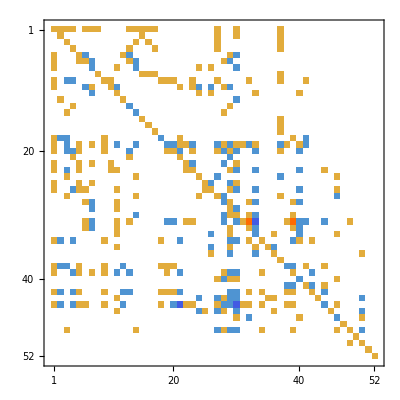
{-Graphics-,MatrixPlot[{12,16,14,15,17,20,24,3,42,30,25,18,19,21,7,4,6,43,45,47,31,33,34,28,26,29,22,32,27,23,50,35,36,44,40,37,5,48,46,13,8,49,41,52,38,39,1,51,9,10,2,11}],MatrixPlot[0]}

```mathematica
Map[MatrixPlot,LUDecomposition[Table[BaseCoeff[k,"C"],{k,treeKeys}]]]
```

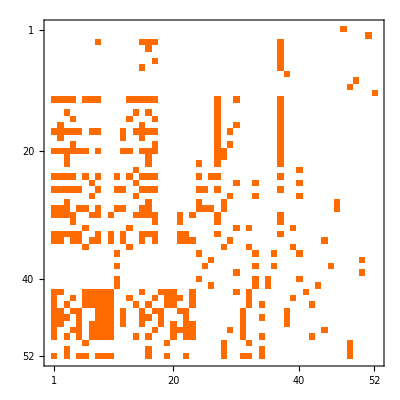

```mathematica
Table[BaseCoeff[k,"C"],{k,treeKeys}]//MatrixPlot
```

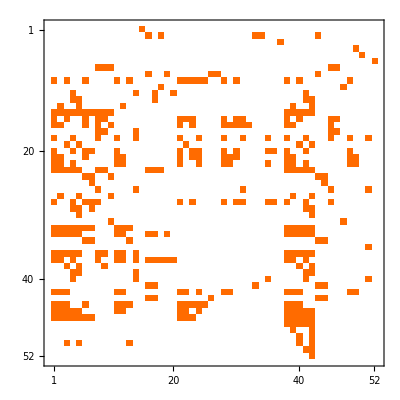

```mathematica
Inverse[Table[TreeCoeff[k],{k,allGraphs5AtomKeys}]]//MatrixPlot
```

MatrixPlot::mat0: Argument {15,34,37,29,50,52,9,27,21,11,16,17,12,1,31,32,46,28,19,48,30,22,18,8,43,36,10,45,7,4,47,33,24,23,35,3,20,2,14,51,44,49,26,25,13,6,38,39,5,40,«2»} at position 1 is not a matrix.

MatrixPlot::mat0: Argument 0 at position 1 is not a matrix.

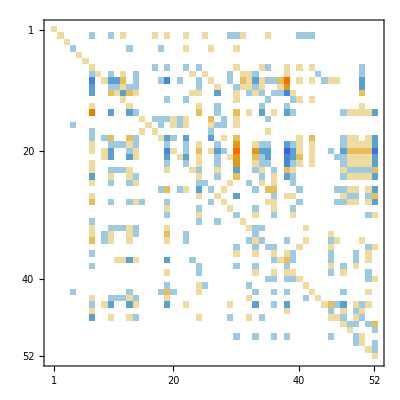
{-Graphics-,MatrixPlot[{15,34,37,29,50,52,9,27,21,11,16,17,12,1,31,32,46,28,19,48,30,22,18,8,43,36,10,45,7,4,47,33,24,23,35,3,20,2,14,51,44,49,26,25,13,6,38,39,5,40,41,42}],MatrixPlot[0]}

```mathematica
Map[MatrixPlot,LUDecomposition[Table[TreeCoeff[k],{k,allGraphs5AtomKeys}]]]
```

## Another experiment

```mathematica
sample=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&& TreeGraphQ[g]&& Max[VertexDegree[g]]≤3 ] &]
```

{28458,28434,28432,27054,26982,26974,26352,26328,26326,26280,26272,26256,26254,26248,22842,22608,22602,22140,22116,22114,21906,21900,21882,21880,21874,20736,20664,20656,20502,20496,20424,20422,20416,20010,20008,19962,19954,19938,19936,19930,19800,19794,19776,19774,19768,19722,19720,19714,9720,9558,9504,9018,8994,8992,8856,8832,8830,8778,8776,7614,7542,7534,7398,7380,7372,7326,7318,6912,6888,6886,6840,6832,6814,6808,6678,6672,6654,6652,6646,6600,6598,6592,3240,3186,3168,3162,3006,3000,2952,2946,2538,2514,2512,2466,2458,2442,2440,2434,2304,2298,2280,2272,2226,2224,2218,1080,1056,1054,1008,1000,984,982,976,846,840,822,820,814,768,766}

```mathematica
Table[FirstNonZero[Reverse[BaseCoeff[k,"C"]]],{k,sample}]//DeleteDuplicates//Sort
```

{7,8,9,10,11,12,13,14,15,16}

```mathematica
sample2=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]}, TreeGraphQ[g] ] &]
```

{29160,29646,29826,29888,29706,29648,29322,29378,29328,29214,29232,29178,29186,29166,29162,29920,30406,30586,30082,29938,29128,28947,28918,28621,28596,28458,28476,28453,28434,28432,31438,31924,31984,31492,31444,32198,32684,31224,30735,30711,27549,27610,27460,27054,27109,27060,27036,26982,26989,26974,28308,27813,27741,26850,26852,26821,26761,26352,26354,26328,26326,26280,26272,26256,26258,26254,26248,35976,36138,36194,36030,35978,36736,36898,35434,35271,35245,38254,38308,39014,37548,33861,33916,33781,34620,33156,33158,33130,33076,22842,23013,23072,22899,22844,22764,22662,22608,22613,22602,23599,23770,23365,22312,22318,22287,22140,22146,22116,22114,22063,21906,21900,21882,21886,21880,21874,25111,25168,24871,25868,24408,24414,24384,24168,20736,20794,20812,20754,20721,20664,20656,20557,20502,20496,20424,20422,20434,20416,21492,21510,21420,21258,20034,20052,20060,20040,20036,20029,20010,20008,19962,19969,19954,19938,19940,19936,19930,19800,19805,19794,19776,19780,19774,19768,19722,19720,19732,19714,49194,49212,49220,49200,49196,49954,49972,48460,48441,48439,51472,51478,52232,50718,46935,46942,46927,47694,46182,46184,46180,46174,56010,56012,56770,55252,58288,59048,53734,42399,42404,42393,43156,41646,41650,41644,41638,44662,40134,40132,40144,40126,9720,9854,9819,9753,9722,9558,9587,9564,9504,9522,10453,10552,10291,9117,9148,9094,9018,9048,8994,8992,8856,8884,8832,8830,8797,8778,8776,11917,11950,11701,12650,11214,11244,11190,10974,7614,7647,7704,7738,7576,7542,7534,7398,7380,7387,7372,7480,7326,7318,8346,8436,8274,8112,6912,6914,6943,6888,6886,7003,7034,6978,6840,6832,6870,6816,6818,6814,6808,6678,6683,6672,6706,6654,6652,6646,6754,6600,6598,6592,16131,16160,16077,16864,15426,15454,15400,15346,18274,13962,13936,14044,13882,3240,3269,3186,3168,3173,3162,3492,3524,3432,3038,3006,3000,2952,2946,3970,3898,4222,3736,2538,2544,2569,2514,2512,2466,2473,2458,2496,2442,2440,2434,2793,2824,2764,2704,2304,2298,2332,2280,2284,2278,2272,2226,2224,2218,5374,5350,5620,5134,1080,1098,1075,1056,1054,1171,1146,1008,1000,984,982,976,1335,1306,1426,1246,846,840,822,820,814,922,768,766,778,760}

```mathematica
Length[sample2]
```

376

```mathematica
Table[FirstNonZero[BaseCoeff[k,"C"]],{k,sample2}]//DeleteDuplicates//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

```mathematica
Sort[Tally[Table[FirstNonZero[BaseCoeff[k,"C"]],{k,sample2}]],If[#1[[2]]==#2[[2]],#1[[1]]<#2[[1]],#1[[2]]<#2[[2]]]&]
```

{{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{50,1},{51,1},{52,1},{12,3},{13,3},{14,3},{15,3},{16,3},{17,3},{18,3},{19,3},{20,3},{21,3},{22,3},{23,3},{24,3},{25,3},{26,3},{27,3},{28,3},{29,3},{30,3},{31,3},{32,3},{33,3},{34,3},{35,3},{36,3},{2,16},{3,16},{4,16},{5,16},{6,16},{7,16},{8,16},{9,16},{10,16},{11,16},{1,125}}

```mathematica
Table[ShowGraph5Least[k],{k,Select[sample2,FirstNonZero[BaseCoeff[#,"C"]]>36&]}]
```

{-Graphics-298881,-Graphics-305861,-Graphics-319840,-Graphics-326841,-Graphics-361940,-Graphics-368980,-Graphics-383080,-Graphics-390141,-Graphics-492201,-Graphics-499721,-Graphics-514780,-Graphics-522321,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
Table[{FirstNonZero[BaseCoeff[k,"C"]],ShowGraph5Least[k]},{k,Sort[Select[sample2,36>=FirstNonZero[BaseCoeff[#,"C"]]≥12&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&]}]
```

{{12,-Graphics-35242},{12,-Graphics-268522},{12,-Graphics-296482},{13,-Graphics-77380},{13,-Graphics-223180},{13,-Graphics-293281},{14,-Graphics-91481},{14,-Graphics-208121},{14,-Graphics-292321},{15,-Graphics-424042},{15,-Graphics-461842},{15,-Graphics-491962},{16,-Graphics-401442},{16,-Graphics-484602},{16,-Graphics-492122},{17,-Graphics-416501},{17,-Graphics-469421},{17,-Graphics-492001},{18,-Graphics-161601},{18,-Graphics-331581},{18,-Graphics-359781},{19,-Graphics-140441},{19,-Graphics-354340},{19,-Graphics-361380},{20,-Graphics-154541},{20,-Graphics-339160},{20,-Graphics-360300},{21,-Graphics-119500},{21,-Graphics-244141},{21,-Graphics-314440},{22,-Graphics-56201},{22,-Graphics-312241},{22,-Graphics-319241},{23,-Graphics-112441},{23,-Graphics-251680},{23,-Graphics-314920},{24,-Graphics-105522},{24,-Graphics-215102},{24,-Graphics-299382},{25,-Graphics-42222},{25,-Graphics-283082},{25,-Graphics-304062},{26,-Graphics-84361},{26,-Graphics-237701},{26,-Graphics-300821},{27,-Graphics-98542},{27,-Graphics-200602},{27,-Graphics-291862},{28,-Graphics-14262},{28,-Graphics-291282},{28,-Graphics-298262},{29,-Graphics-28241},{29,-Graphics-276101},{29,-Graphics-297061},{30,-Graphics-70341},{30,-Graphics-230721},{30,-Graphics-293781},{31,-Graphics-537342},{31,-Graphics-552522},{31,-Graphics-560102},{32,-Graphics-446621},{32,-Graphics-507181},{32,-Graphics-514721},{33,-Graphics-431562},{33,-Graphics-476942},{33,-Graphics-499542},{34,-Graphics-182741},{34,-Graphics-375481},{34,-Graphics-382541},{35,-Graphics-168641},{35,-Graphics-346201},{35,-Graphics-367361},{36,-Graphics-126502},{36,-Graphics-258682},{36,-Graphics-321982}}

```mathematica
BrokenCycleQ[g_]:=Block[{},
VertexCount[g]==1||
Fold[And,Table[EdgeQ[g,n->n+1],{n,1,VertexCount[g]-1}]]
]
```

```mathematica
BrokenCycle[allGraphs5[19936,"graph"]]
```

True

```mathematica
Table[{FirstNonZero[BaseCoeff[k,"C"]],ShowGraph5Least[k]},{k,Sort[Select[sample2,11>=FirstNonZero[BaseCoeff[#,"C"]]≥1&& BrokenCycle[allGraphs5[#,"graph"]] &],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&]}]
```

{{1,-Graphics-199365},{2,-Graphics-199403},{3,-Graphics-200293},{4,-Graphics-199692},{5,-Graphics-268213},{6,-Graphics-222871},{7,-Graphics-207212},{8,-Graphics-461803},{9,-Graphics-331301},{10,-Graphics-243842},{11,-Graphics-214203}}

```mathematica
Table[{FirstNonZero[BaseCoeff[k,"C"]],ShowGraph5Least[k]},{k,Sort[Select[sample2,(36>=FirstNonZero[BaseCoeff[#,"C"]]≥12)&& BrokenCycle[allGraphs5[#,"graph"]]&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&]}]
```

{{12,-Graphics-268522},{13,-Graphics-223180},{14,-Graphics-208121},{15,-Graphics-461842},{16,-Graphics-484602},{17,-Graphics-469421},{18,-Graphics-331581},{19,-Graphics-354340},{20,-Graphics-339160},{21,-Graphics-244141},{22,-Graphics-312241},{23,-Graphics-251680},{24,-Graphics-215102},{25,-Graphics-283082},{26,-Graphics-237701},{27,-Graphics-200602},{28,-Graphics-291282},{29,-Graphics-276101},{30,-Graphics-230721},{31,-Graphics-552522},{32,-Graphics-507181},{33,-Graphics-476942},{34,-Graphics-375481},{35,-Graphics-346201},{36,-Graphics-258682}}

```mathematica
Table[{FirstNonZero[BaseCoeff[k,"C"]],ShowGraph5Least[k]},{k,Sort[Select[sample2,BrokenCycle[allGraphs5[#,"graph"]]&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&]}]
```

{{1,-Graphics-199365},{2,-Graphics-199403},{3,-Graphics-200293},{4,-Graphics-199692},{5,-Graphics-268213},{6,-Graphics-222871},{7,-Graphics-207212},{8,-Graphics-461803},{9,-Graphics-331301},{10,-Graphics-243842},{11,-Graphics-214203},{12,-Graphics-268522},{13,-Graphics-223180},{14,-Graphics-208121},{15,-Graphics-461842},{16,-Graphics-484602},{17,-Graphics-469421},{18,-Graphics-331581},{19,-Graphics-354340},{20,-Graphics-339160},{21,-Graphics-244141},{22,-Graphics-312241},{23,-Graphics-251680},{24,-Graphics-215102},{25,-Graphics-283082},{26,-Graphics-237701},{27,-Graphics-200602},{28,-Graphics-291282},{29,-Graphics-276101},{30,-Graphics-230721},{31,-Graphics-552522},{32,-Graphics-507181},{33,-Graphics-476942},{34,-Graphics-375481},{35,-Graphics-346201},{36,-Graphics-258682},{37,-Graphics-492201},{38,-Graphics-560121},{39,-Graphics-514780},{40,-Graphics-499721},{41,-Graphics-361940},{42,-Graphics-383080},{43,-Graphics-368980},{44,-Graphics-319840},{45,-Graphics-326841},{46,-Graphics-305861},{47,-Graphics-298881},{48,-Graphics-582881},{49,-Graphics-567701},{50,-Graphics-522321},{51,-Graphics-390141}}

```mathematica
allTreeKeys2=Sort[
Select[sample2,BrokenCycle[allGraphs5[#,"graph"]]&],FirstNonZero[BaseCoeff[#1,"C"]]<FirstNonZero[BaseCoeff[#2,"C"]]&]
```

{19936,19940,20029,19969,26821,22287,20721,46180,33130,24384,21420,26852,22318,20812,46184,48460,46942,33158,35434,33916,24414,31224,25168,21510,28308,23770,20060,29128,27610,23072,55252,50718,47694,37548,34620,25868,49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014,59048}

```mathematica
Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==1&]
```

{59048}

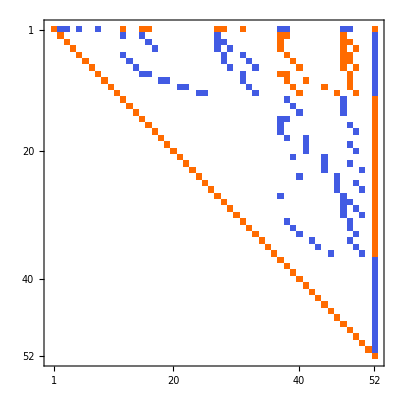

```mathematica
Table[BaseCoeff[k,"E"],{k,allTreeKeys2}]//MatrixPlot
```

```mathematica
Table[BaseCoeff[k,"E"],{k,allTreeKeys2}]//MatrixForm
```

(1 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Table[allGraphs5[k,"vertexsets"],{k,allGraphs5TreeKeys}]//DeleteDuplicates//Length
```

52